```mathematica
R[t_]=Sqrt[t] {Cos[t],Sin[t]}
```

{√t cos(t),√t sin(t)}

```mathematica
v[t_]=R'[t]
```

{(cos(t))/(2 √t)-√t sin(t),(sin(t))/(2 √t)+√t cos(t)}

```mathematica
RObs={3.5,-2.5}
```

{3.5,-2.5}

```mathematica
p[t_]=R[t]-RObs
```

{√t cos(t)-3.5,√t sin(t)+2.5}

```mathematica
pHat[t_]=p[t]/Sqrt[p[t].p[t]]
```

{(√t cos(t)-3.5)/(√((√t sin(t)+2.5)^2+(√t cos(t)-3.5)^2)),(√t sin(t)+2.5)/(√((√t sin(t)+2.5)^2+(√t cos(t)-3.5)^2))}

```mathematica
t0=4
```

4

```mathematica
pOrigHat = -RObs/Sqrt[RObs.RObs]
```

{-0.813733,0.581238}

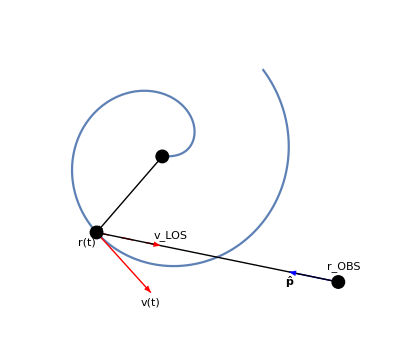

```mathematica
ParametricPlot[R[t],{t,0,7},PlotRange->{{-2.5,4},{-3,2.5}},
Axes->None,Frame->None,AspectRatio->5.5/6.5,
Epilog->{
Thick,Blue,Arrow[{RObs,RObs+pHat[t0]}],
Thick,Black,Arrow[{{0,0},R[t0]}],
Thick,Red,Arrow[{R[t0],R[t0]+0.8v[t0]}],
Thick,Red,{Dashing[Medium],Arrow[{R[t0],R[t0]+0.8(v[t0].pHat[t0])pHat[t0]}]},
Thin,Black,Line[{RObs,R[t0]}],
PointSize[0.025],Point[RObs],Point[R[t0]],Point[{0,0}],
Text[Style["r(t)",{Italic,Medium}],R[t0]-{0.2,0.2}],
Text[Style["r_OBS",{Medium}],RObs+{0.1,0.3}],
Text[Style["v_LOS",{Medium}],R[t0]+0.8(v[t0].pHat[t0])pHat[t0]+{0.2,0.2}],
Text[Style["p̂",{Bold,Italic,Medium}],RObs+pHat[t0]-{0.0,0.2}],
Text[Style["v(t)",{Italic,Medium}],R[t0]+0.8v[t0]+{0,-0.2}]
}]
```

```mathematica
Integrate[x^5 Exp[-x^2]Cos[x^2],x]
```

1/4 ⅇ^(-x^2) ((x^2+1)^2 sin(x^2)-(x^4-1) cos(x^2))

```mathematica
Integrate[Cos[x]^4Sin[x]^6,x]
```

(3 x)/256-1/512 sin(2 x)-1/256 sin(4 x)+(sin(6 x))/1024+(sin(8 x))/2048-(sin(10 x))/5120

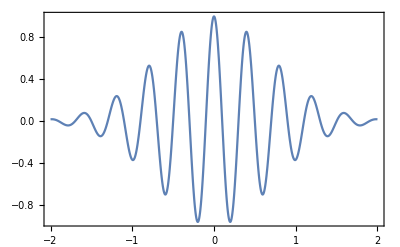

```mathematica
Plot[Cos[5Pi t]Exp[-t^2],{t,-2,2}]
```